```mathematica
Clear["Global`*"]
```

```mathematica
(*Физические константы*)
c=3 10^8;(*м/с*)
h=6.63 10^-34;(*Планк*)
NN=6.62 10^22 ;(*1/м^3*)(*Перевод  концентрации из ppm в 1/м^3*)
```

```mathematica
(*Параметры среды*)
d=10.5 10^-6;(*m*) (*MFD*)
A=N[(π d^2)/4];(*m^2*) (*Mode Area*)
α =6 10^-3; (*absorption*)(*1/m*)(* ~22dB/km *) (*Smith1972 pp4*) (*!!!*)
τ=1.45 10^-3;(*с*)
Δν=13.; (*GHz*)(*сдвиг ВРМБ*)
gb =N[5. 10^-12]; (*m/W*)(*ВРМБ усиление*)
N0=5400;
NN0[z_,L1_,L2_]:=N0(HeavisideTheta[z-L1])(1-HeavisideTheta[z-(L1+L2)]);(*ppm*)
```

```mathematica
(*Длины волн и коэффициенты перевода плотности фотонов в мощность P=ρ*W *)
λs=1064;(*нм*)
λp=1030;(*нм*)
λSt=(c λs)/(c-Δν λs);(*нм*)
Ws=(A h c NN)/(λs 10^-9);
Wp=(A h c NN)/(λp 10^-9);
WSt=(A h c NN)/(λSt 10^-9);
```

```mathematica
(*Сечения поглощения и люминесценции*)
(σ=Import[NotebookDirectory[]<>"CrossSection.xls",{"DataLegacy"}][[1,5;;,{12,15,16}]])//TableForm;
σe=Interpolation[σ[[All,{1,2}]],InterpolationOrder->1];
σa=Interpolation[σ[[All,{1,3}]],InterpolationOrder->1];
σs12=σa[λs]NN;
σs21=σe[λs]NN;
σp12=σa[λp]NN;
σp21=σe[λp]NN;
σSt12=σa[λSt]NN;
σSt21=σe[λSt]NN;
```

```mathematica
(*Начальные параметры усилителя*)
L1= 1.7; (*m*) (*Пассивное волокно на входе в усилитель*)
L2=3.5;(*m*)(*Активное волокно*)
L3=2.;(*m*)(*Пассивное волокно на выходе усилителя*)
L=L1+L2+L3; (*m*) (*Длина всего оптического тракта*)
Ps0=0.180; (*Вт*) (*Сигнал на входе в усилитель*)
P1030Table = {0.98,1.74,2.5,3.24,4.0,4.7,5.23,6.25,7.2,8.2,9.25,10.4,11.06,11.6,11.8,12.2,12.6,13.5,14.5,15.0,15.95,16.85,17.54,18.06,18.23,18.8,20.3,21.2,22.4,23.3,24.25};
(BR193=Import[NotebookDirectory[]<>"Книга1.xlsx",{"DataLegacy"}][[1,4;;,{3,12}]])//TableForm;
BR193[[All,2]]=BR193[[All,2]]/1000.-0.2;
```

```mathematica
(*Скоростные уравнения с учетом ВРМБ*)
eqns1={
0==Pp[z]/Wp(σp12 N1[z]-σp21 N2[z])+Ps[z]/Ws(σs12 N1[z]-σs21 N2[z])+PSt[z]/WSt(σSt12 N1[z]-σSt21 N2[z])-N2[z]/τ,
Ps'[z]==Ps[z](σs21 N2[z]-σs12 N1[z])-α Ps[z]-gb/A Ps[z]PSt[z],
Pp'[z]==Pp[z](σp21 N2[z]-σp12 N1[z])-α Pp[z],
PSt'[z]==-gb/A PSt[z] Ps[z]+α PSt[z]-PSt[z](σSt21 N2[z]-σSt12 N1[z]),
N1[z]+N2[z]==NN0[z,L1,L2]};
sol0=Solve[eqns1[[{1,5}]],{N1[z],N2[z]}][[1]];
eqns2=Simplify[eqns1[[{2,3,4}]]/.%];
sol[Ppump_]:=NDSolve[{eqns2,PSt[L]==bin Ps[L],Pp[0]==Ppump,Ps[0]==Ps0},{Pp,Ps,PSt},{z,0,L},AccuracyGoal->8][[1]];
```

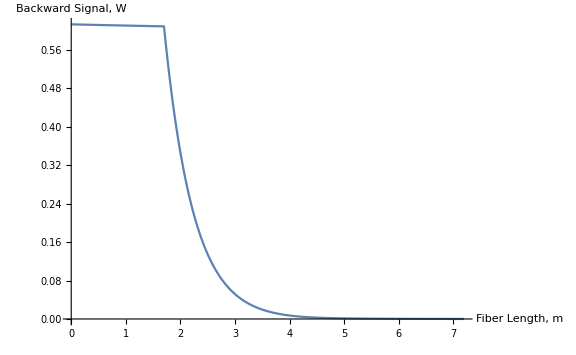

```mathematica
bin=4. 10^-6;
Plot[Evaluate[PSt[z]/.sol[24.25]],{z,0,L},PlotRange->All,AxesLabel->{"Fiber Length, m","Backward Signal, W"},ImageSize->Large,LabelStyle->Directive[Black,Bold,Medium]]
```

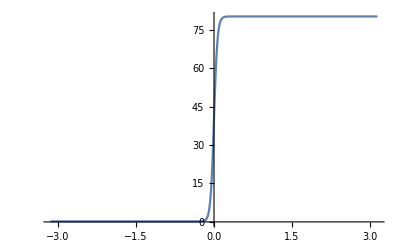

```mathematica
Plot[80(Tanh[15(z)]+1)/2+0.2,{z, -π, π}]
```